### Enquist model and HIREC

```mathematica
WS=w0+Qt b ;    (*fitness social learner pre hirec*)
WI=w0+s b-c;   (*fitness individual learner pre hirec*)
WSI=w0+ Qt b  + (1- Qt)(s b-c);   (*fitness critical SL learner pre hirec*)
Qt=(1-u)( (1-p-m)s+(p+m)Qtm1 + m s(1-Qtm1)); 
(*prob of acquiring adaptive behavior recursion*)
```

```mathematica
FullSimplify[Solve[Qt==Qtm1,Qtm1]] (*solve for equilibria for Qhat, frequency of adaptive behavior in population*)
```

```mathematica
Qhat=(s (-1+p+u-p u))/(-1+p+m (-1+s) (-1+u)-p u);
```

```mathematica
Simplify[Solve[{WS==WI,Qt==Qtm1},{p,Qtm1}]/.m->0](*solve equilibria when no critical social learners in population (m=0), same as Rogers*)
```

```mathematica
phatnoCL=(c-b s u)/(c-c u);
QhatnoCL=-c/b+s;
```

```mathematica
(*When does a critical social learner beat pure social learner?*)
Simplify[Solve[{WS==WSI,Qt==Qtm1},{p,Qtm1}]/.m->0] (*only when q=1 are these equal, non interesting internal equlibrium*)
phatnoIL=(1+s (-1+u))/((-1+s) (-1+u));
QhatnoIL=1;
```

```mathematica
(*When does a critical social learner beat individual learner?*)
```

```mathematica
(*Pure SL is never an ESS, so p=0 and we can simplify Qhat*)
Simplify[ Qhat /.p->0]
```

```mathematica
QhatnoSL=(s (-1+u))/(-1+m (-1+s) (-1+u));
Simplify[QhatnoSL /.m -> 1]
QhatpureCL = (s-s u)/(s+u-s u);
```

```mathematica
(*Fitness Difference*)
WSI -WI /. {Qtm1-> QhatpureCL,m->1, p-> 0}
```

c-b s+b (1-u) ((s-s u)/(s+u-s u)+s (1-(s-s u)/(s+u-s u)))+(-c+b s) (1-(1-u) ((s-s u)/(s+u-s u)+s (1-(s-s u)/(s+u-s u))))

```mathematica
Simplify[Solve[WI==WSI,c]/.{ Qtm1 -> Qhat} ] 

(*only when q=1 are these equal*)
```

```mathematica
]
```

1+1.6 (0.5 (1-m)+0.5 (1+0.4/(-1.+0.4 m)) m-(0.4 m)/(-1.+0.4 m))-0.5 (1-0.8 (0.5 (1-m)+0.5 (1+0.4/(-1.+0.4 m)) m-(0.4 m)/(-1.+0.4 m)))

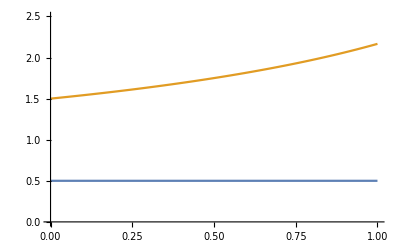

```mathematica
Qplot =  Qhat/. {p->0,b-> 2,c->1.5,u->0.2,s->0.5 , w0 ->1};
subs={p->0,b-> 2,c->1.5,u->0.2,s->0.5 , w0 ->1, Qtm1 -> Qplot };

WIplot =WI/.subs;
WSIplot =WSI/.subs;

WSIplot
Plot[{WIplot,WSIplot} ,{m, 0,1} , PlotRange->{0,2.5}  ]
```

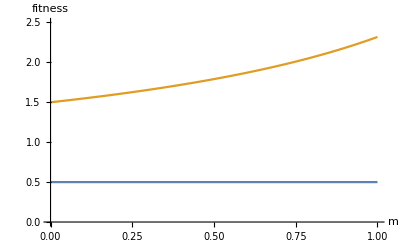

```mathematica
Show[%738,AxesLabel->{HoldForm[m],HoldForm[fitness]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/Users/brendanbarrett/Dropbox/Social Learning & HIREC/RECit Rogers/enquist bjb version.pdf",%740,"PDF"]
```

/Users/brendanbarrett/Dropbox/Social Learning & HIREC/RECit Rogers/enquist bjb version.pdf

```mathematica
(* POST HIREC ANALYSIS*)
```